```mathematica
ϕ[ω_,a_]:=a*ω
```

```mathematica
a[ω_,t_,ϕ[ω_,a_],α_]:=1/2*(Sin[ω*t]+1/4Sin[ω*t+ϕ])*Cos[α]
```

```mathematica
b[ω_,t_,ϕ[ω_,a_],α_]:=1/2*Cos[ω*t+ϕ]*Sin[α]
```

```mathematica
amean[ω_,ϕ[ω_,a_],α_]=ω/(2*Pi)*Integrate[a[ω,t,ϕ,α]^2,{t,0,2*Pi/ω}]
```

1/128 Cos[α]^2 (17+8 Cos[ϕ])

```mathematica
bmean[ω_,ϕ[ω_,a_],α_]=ω/(2*Pi)*Integrate[b[ω,t,ϕ,α]^2,{t,0,2*Pi/ω}]
```

Sin[α]^2/8

```mathematica
Manipulate[Plot[{a[1,t,ϕ],b[1,t,ϕ]},{t,-10,10}],{ϕ,0,2*Pi}]
```

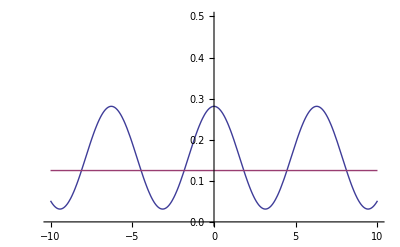

```mathematica
Plot[{amean[1,ϕ],bmean[1,ϕ]},{ϕ,-10,10},PlotRange->{0,0.5}]
```

```mathematica
Manipulate[Plot[{amean[ω,ϕ,α],bmean[ω,ϕ,α]},{ω,1,2},PlotRange->{0,0.5}],{ϕ,0,2*Pi},{α,0,2*Pi}]
```

```mathematica
Manipulate[Plot[{amean[ω,ϕ[ω,5],α],bmean[ω,ϕ[ω,5],α]},{ω,1,2},PlotRange->{0,0.5}],{α,0,2*Pi}]
```

```mathematica
Manipulate[ParametricPlot[{amean[ω,ϕ[ω,5],α],bmean[ω,ϕ[ω,5],α]},{ω,10000,20000}],{α,0,2*Pi}]
```